# Advection Equation CFD

### How do I use this Code?

This code is meant primarily for time evolution analysis of CFD operators. To use:
1. Clear using the block below
2. Run the “Defining Coefficients” block. This contains coefficients found outside of this code (Primarily in Tyler’s paper) and defines them for use in the operators. If you instead want to use your own coefficients, define a new variable in this block and follow the pattern of the other variables. Make sure to include your new variable in the Clear function at the top.
3. Run the “LHS and RHS Matrix Modules” block, which will define the modules used in the construction of your operators.
4. If you are wanting to run the 1D Advection equation code, execute the “Advection Equation Setup” block to initialize more helpful modules and variables needed. If you want to do the heat equation, run the “Diffusion Equation Setup” block instead. If you are just looking at E. Spectra, skip to the one you want to look at.
5. Run the Operation that you are looking at (Ex. “T4 Boundary Conditions (Fixed Left)”) or create your own in the same pattern. Change the number in the update function to be the number of “seconds” you want each step to run for.

```mathematica
Clear["`*"];
```

## Essential Modules and Setup

### Defining Coefficients

```mathematica
Clear[coeffP12,coeffP6,coeffP8,coeffT4,coeffT6,coeffP10,coeffT8,coeffT42D];

coeffVariables={
α,β,
α12,β12,
α21,α22,β22,
β31,α31,α32,β32,
β41,α41,α42,β42,
a,b,c,d,
a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1,
a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2,
a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3,
a4,b4,c4,d4,e4,f4,g4,h4,i4,j4,k4
};
coeffAllZero={
α->0,β->0,
α12->0,β12->0,
α21->0,α22->0,β22->0,
β31->0,α31->0,α32->0,β32->0,
β41->0,α41->0,α42->0,β42->0,
a->0,b->0,c->0,d->0,
a1->0,b1->0,c1->0,d1->0,e1->0,f1->0,g1->0,h1->0,i1->0,j1->0,k1->0,
a2->0,b2->0,c2->0,d2->0,e2->0,f2->0,g2->0,h2->0,i2->0,j2->0,k2->0,
a3->0,b3->0,c3->0,d3->0,e3->0,f3->0,g3->0,h3->0,i3->0,j3->0,k3->0,
a4->0,b4->0,c4->0,d4->0,e4->0,f4->0,g4->0,h4->0,i4->0,j4->0,k4->0
};

coeffNJP8=Join[{a->40/27,b->25/54,α->4/9,β->1/36,a1->-79/20,b1->-77/5,c1->55/4,d1->20/3,e1->-5/4,f1->1/5,g1->-1/60,a2->-257/1080,b2->-107/60,c2->-5/24,d2->55/27,e2->5/24,f2->-1/60,g2->1/1080,a3->-34/675,b3->-127/225,c3->-7/12,d3->20/27,e3->4/9,f3->1/75,g3->-1/2700,a4->-1/600,b4->-101/600,c4->-17/24,d4->0,e4->17/24,f4->101/600,g4->1/600,α12->12,β12->15,α21->1/18,α22->5/2,β22->10/9,β31->1/90,α31->4/15,α32->8/9,β32->1/6,β41->1/20,α41->1/2,α42->1/2,β42->1/20},coeffAllZero];

coeffT4=Join[{α->1/4,α12->3,a->3/2,a1->-17/6,b1->3/2,c1->3/2,d1->-1/6},coeffAllZero];

coeffT42D=Join[{α->1/10,α12->10,a->6/5,a1->145/12,b1->-76/3,c1->29/2,d1->-4/3,e1->1/12},coeffAllZero];

coeffT6=Join[{
α->1/3,
α12->5,
α21->1/8,α22->3/4,
a->14/9,b->1/9,c->0,d->0,
a1->-197/60,b1->-5/12,c1->5,d1->-5/3,e1->5/12,f1->-1/20,
a2->-43/96,b2->-5/6,c2->9/8,d2->1/6,e2->-1/96
},coeffAllZero];

coeffT8=Join[{
α->3/8,
α12->7,
α21->1/12,α22->5/4,
α31->13/55,α32->6/11,
a->25/16,b->1/5,c->-1/80,
a1->-503/140,b1->-63/20,c1->21/2,d1->-35/6,e1->35/12,f1->-21/20,g1->7/30,h1->-1/42,
a2->-79/240,b2->-77/60,c2->55/48,d2->5/9,e2->-5/48,f2->1/60,g2->-1/720,
a3->-1/66,b3->-2051/3300,c3->-53/132,d3->31/33,e3->7/66,f3->-1/132,g3->1/3300
},coeffAllZero];


coeffP6=Join[{
α->17/57,β->-1/114,
α12->8,β12->6,
a->30/19,b->0,c->0,d->0,
a1->-43/12,b1->-20/3,c1->9,d1->4/3,e1->-1/12
},coeffAllZero];

coeffP8=Join[{
α->4/9,β->1/36,
α12->12,β12->15,
α21->2,α22->2/3,β22->1/15,
a->40/27,b->25/54,
a1->-79/20,b1->-77/5,c1->55/4,d1->20/3,e1->-5/4,f1->1/5,g1->-1/60,
a2->-247/900,b2->-19/12,c2->1/3,d2->13/9,e2->1/12,f2->-1/300
},coeffAllZero];

coeffP10={
α->1/2,β->1/20,
α12->16,β12->28,
α21->1/21,α22->3,β22->5/3,
β31->1/90,α31->4/15,α32->8/9,β32->1,
β41->0,α41->0,α42->0,β42->0,
a->17/12,b->101/150,c->1/100,d->0,
a1->-1181/280,b1->-892/35,c1->77/5,d1->56/3,e1->-35/6,f1->28/15,g1->-7/15,h1->8/105,i1->-1/168,j1->0,k1->0,
a2->-544/2581,b2->-39/20,c2->-17/20,d2->95/36,e2->5/12,f2->-1/20,g2->1/180,h2->-1/2940,i2->0,j2->0,k2->0,
a3->-34/675,b3->-127/225,c3->-7/12,d3->20/27,e3->4/9,f3->1/75,g3->-1/2700,h3->0,i3->0,j3->0,k3->0,
a4->0,b4->0,c4->0,d4->0,e4->0,f4->0,g4->0,h4->0,i4->0,j4->0,k4->0
};

coeffP12={
α->8/15,β->1/15,
α12->20,β12->45,
α21->1/27,α22->4,β22->28/9,
β31->1/168,α31->4/21,α32->4/3,β32->5/12,
β41->1/42,α41->1/3,α42->5/6,β42->1/6,
a->308/225,b->182/225,c->4/175,d->-1/1575,
a1->-1590/359,b1->-4609/126,c1->711/56,d1->40,e1->-35/2,f1->42/5,g1->-7/2,h1->8/7,i1->-15/56,j1->5/126,k1->-1/360,
a2->-857/4963,b2->-621/280,c2->-83/35,d2->511/135,e2->7/6,f2->-7/30,g2->7/135,h2->-1/105,i2->1/840,j2->-1/13608,k2->0,
a3->-115/4024,b3->-1019/2205,c3->-19/20,d3->23/45,e3->125/144,f3->1/15,g3->-1/180,h3->1/2205,i3->-1/47040,j3->0,k3->0,
a4->-1/1680,b4->-193/2205,c4->-107/180,d4->-9/20,e4->25/36,f4->19/45,g4->1/60,h4->-1/1260,i4->1/35280,j4->0,k4->0
};
```

### LHS and RHS Matrix Modules

```mathematica
LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32},
{0,β41,α41,1,α42,β42},
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1},
{a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2},
{a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3},
{a4,b4,c4,d4,e4,f4,g4,h4,i4,j4,k4}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
]

InsideOneSidedBoundaryLHS[M_,row_,borders_,coeff_]:=Module[{newM,size=Length[M]},
newM=M;

For[i=1,i<=borders,i++,
newM[[row+i-1]]=ConstantArray[0,size];
newM[[row-i]]=ConstantArray[0,size];
For[j=1,j<=Length[LHSBorders[[i]]],j++,
newM[[row+i-1,j+row-1]]=LHSBorders[[i,j]]/.coeff;
newM[[row-i,row-j]]=LHSBorders[[i,j]]/.coeff;
]
];

newM[[row+1,row-1]]=0;
newM[[row+2,row-1]]=0;
newM[[row+1,row-2]]=0;

newM[[row-2,row]]=0;
newM[[row-3,row]]=0;
newM[[row-2,row+1]]=0;

newM
]

PeriodicLHS[size_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β,
Band[{1,size}]->α,
Band[{1,size-1}]->β,
Band[{size,1}]->α,
Band[{size-1,1}]->β
}/.coeff,{size,size}];
M
]

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a/2,
Band[{3,1}]->-b/4,
Band[{4,1}]->-c/6,
Band[{5,1}]->-d/8,
Band[{1,2}]->a/2,
Band[{1,3}]->b/4,
Band[{1,4}]->c/6,
Band[{1,5}]->d/8
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]


RHSMatrix2D[size_,borders_,coeff_,H_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->-2(a+b 1/4+c 1/9+d 1/16),
Band[{2,1}]->a,
Band[{3,1}]->b/(4),
Band[{4,1}]->c/(9),
Band[{5,1}]->d/(16),
Band[{1,2}]->a,
Band[{1,3}]->b/(4),
Band[{1,4}]->c/(9),
Band[{1,5}]->d/(16)
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]

InsideOneSidedBoundaryRHS[M_,row_,borders_,coeff_]:=Module[{newM,size=Length[M]},
newM=M;

For[i=1,i<=borders,i++,
newM[[row+i-1]]=ConstantArray[0,size];
newM[[row-i]]=ConstantArray[0,size];
For[j=1,j<=Length[RHSBorders[[i]]],j++,
newM[[row+i-1,j+row-1]]=RHSBorders[[i,j]]/.coeff;
newM[[row-i,row-j]]=-RHSBorders[[i,j]]/.coeff;
]
];

newM[[row+1,row-1]]=0;
newM[[row+2,row-1]]=0;
newM[[row+3,row-1]]=0;
newM[[row+1,row-2]]=0;
newM[[row+2,row-2]]=0;
newM[[row+1,row-3]]=0;

newM[[row-2,row]]=0;
newM[[row-3,row]]=0;
newM[[row-4,row]]=0;
newM[[row-2,row+1]]=0;
newM[[row-3,row+1]]=0;
newM[[row-2,row+2]]=0;

newM
]

PeriodicRHS[size_,coeff_]:=Module[{M,H},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a/2,
Band[{3,1}]->-b/4,
Band[{4,1}]->-c/6,
Band[{5,1}]->-d/8,
Band[{1,2}]->a/2,
Band[{1,3}]->b/4,
Band[{1,4}]->c/6,
Band[{1,5}]->d/8,
Band[{1,size}]->-a/2,
Band[{1,size-1}]->-b/4,
Band[{1,size-2}]->-c/6,
Band[{1,size-3}]->-d/8,
Band[{size,1}]->a/2,
Band[{size-1,1}]->b/4,
Band[{size-2,1}]->c/6,
Band[{size-3,1}]->d/8
}/.coeff,{size,size}];

M
]

DirichletBoundary[M_,LeftHandSide_,left_,right_]:=Module[{newM,size},
newM=M;
size=Length[newM[[1]]];
If[left,newM[[1]]=ConstantArray[0,size]];
If[right,newM[[size]]=ConstantArray[0,size]];
newM=Transpose[newM];
If[left,newM[[1]]=ConstantArray[0,size]];
If[right,newM[[size]]=ConstantArray[0,size]];
newM=Transpose[newM];
If[LeftHandSide,
If[left,newM[[1,1]]=1];
If[right,newM[[size,size]]=1];
];
newM
]



L=LHSMatrix[25,3,coeffNJP8];
R=RHSMatrix[25,3,coeffNJP8];

L//MatrixForm
R//MatrixForm

(*l=PeriodicLHS[25,{}];
r=PeriodicRHS[25,{}];
l=InsideOneSidedBoundaryLHS[l,12,1,{}];
r=InsideOneSidedBoundaryRHS[r,12,1,{}];
l//MatrixForm
r//MatrixForm*)
```

(1 | 12 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/18 | 1 | 5/2 | 10/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/90 | 4/15 | 1 | 8/9 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 4/9 | 1 | 4/9 | 1/36 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 8/9 | 1 | 4/15 | 1/90
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10/9 | 5/2 | 1 | 1/18
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15 | 12 | 1)

(-79/20 | -77/5 | 55/4 | 20/3 | -5/4 | 1/5 | -1/60 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-257/1080 | -107/60 | -5/24 | 55/27 | 5/24 | -1/60 | 1/1080 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-34/675 | -127/225 | -7/12 | 20/27 | 4/9 | 1/75 | -1/2700 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25/216 | -20/27 | 0 | 20/27 | 25/216 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2700 | -1/75 | -4/9 | -20/27 | 7/12 | 127/225 | 34/675
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/1080 | 1/60 | -5/24 | -55/27 | 5/24 | 107/60 | 257/1080
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/60 | -1/5 | 5/4 | -20/3 | -55/4 | 77/5 | 79/20)

## Advection Equation

### Advection Equation Setup

```mathematica
Clear[Δt,σ,n,h,timeVal,solution,ϕ,reset,updateFunction,plotFunction,ctq];

(*Initialize Parameters*)
Δt=0.0001;
waveSpeed=0.05;
n=401;
h=1/(n-1);
timeVal=0;

(*Analytic Solution*)
solution[x_,t_]:=If[x>waveSpeed t,Sin[10π (x-waveSpeed t)],0];

(*Initial discretized wave*)
ϕ=Array[Sin[10 π #]&,n,{0,1}];

reset[]:=Module[{},
timeVal=0;
ϕ=Array[Sin[10 π #]&,n,{0,1}];
]

updateFunction[steps_,Q_]:=Module[{ctQ},
ctQ=waveSpeed Δt Q;
For[i=0,i<steps,i++,
timeVal+=Δt;
ϕ=ϕ-ctQ.ϕ;
];
]

plotFunction[range_]:=Module[{},
normalizePlot={};
For[i=1,i<=n,i++,AppendTo[normalizePlot,{(i-1)/(n-1),ϕ[[i]]}]];
Print["At T = "<>ToString[timeVal]<>"s:"];
Show[Plot[solution[x,timeVal],{x,0,1},PlotRange->range,PlotStyle->Gray],
ListPlot[normalizePlot,PlotRange->range,Joined->True]]
]
```

### Convergence Testing

```mathematica
Clear[u,v,w,n1,n2,n3,h1,h2,h3,ϕ1,ϕ2,ϕ3,LHS1,LHS2,LHS3,RHS1,RHS2,RHS3,Q1,Q2,Q3,ctq1,ctq2,ctq3];


(* Define Subscript[u, i]^n(t) *)
n1=400;
h1=1/(n1-1);
ϕ1=Array[Sin[10 π #]&,n1,{0,1}];

(* Set Up Derivative Operator Q1 *)
LHS1=PeriodicLHS[n1,coeffT4];
RHS1=PeriodicRHS[n1,coeffT4];
RHS1=1/h1 RHS1;
LHS1//MatrixForm;
RHS1//MatrixForm;
Q1=Inverse[LHS1].RHS1;
ctQ1=waveSpeed Δt Q1;

(* Define Subscript[v, i]^n(t) *)
n2=200;
h2=1/(n2-1);
ϕ2=Array[Sin[10 π #]&,n2,{0,1}];

(* Set Up Derivative Operator Q1 *)
LHS2=PeriodicLHS[n2,coeffT4];
RHS2=PeriodicRHS[n2,coeffT4];
RHS2=1/h2 RHS2;
LHS2//MatrixForm;
RHS2//MatrixForm;
Q2=Inverse[LHS2].RHS2;
ctQ2=waveSpeed Δt Q2;

(* Define Subscript[w, i]^n(t) *)
n3=100;
h3=1/(n3-1);
ϕ3=Array[Sin[10 π #]&,n3,{0,1}];

(* Set Up Derivative Operator Q1 *)
LHS3=PeriodicLHS[n3,coeffT4];
RHS3=PeriodicRHS[n3,coeffT4];
RHS3=1/h3 RHS3;
LHS3//MatrixForm;
RHS3//MatrixForm;
Q3=Inverse[LHS3].RHS3;
ctQ3=waveSpeed Δt Q3;


(* Update All Functions *)
For[i=0,i<10/Δt,i++,
ϕ1=ϕ1-ctQ1.ϕ1;
ϕ2=ϕ2-ctQ2.ϕ2;
ϕ3=ϕ3-ctQ3.ϕ3;
];

ϕ1//MatrixForm
ϕ2//MatrixForm
ϕ2//MatrixForm
```

### T4 Periodic Boundary

At T = 2.s:

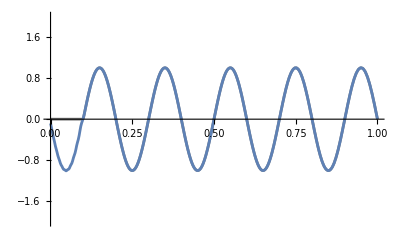

At T = 17.s:

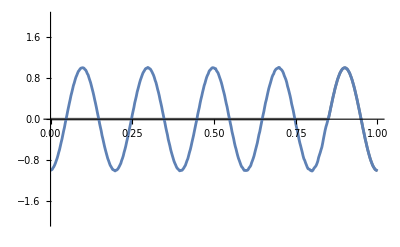

```mathematica
Clear[LHS,RHS,Q];

LHS=PeriodicLHS[n,coeffT4];

RHS=PeriodicRHS[n,coeffT4];

(*LHS=InsideOneSidedBoundaryLHS[LHS,70,1,coeffT4];
RHS=InsideOneSidedBoundaryRHS[RHS,70,1,coeffT4];*)

RHS=1/h RHS;

LHS//MatrixForm;
RHS//MatrixForm;

Q=Inverse[LHS].RHS;

reset[]

updateFunction[2/Δt,Q];
plotFunction[{-2,2}]

(*reset[]*)

updateFunction[15/Δt,Q];
plotFunction[{-2,2}]
```

### T8 Periodic Boundary

At T = 10.s:

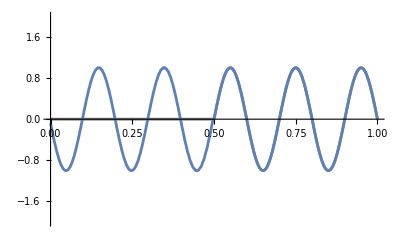

$Aborted

At T = 12.0497s:

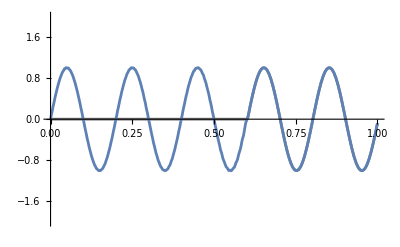

```mathematica
Clear[LHS,RHS,Q];

LHS=PeriodicLHS[n,coeffT8];

RHS=PeriodicRHS[n,coeffT8];

(*LHS=InsideOneSidedBoundaryLHS[LHS,70,3,coeffT8];
RHS=InsideOneSidedBoundaryRHS[RHS,70,3,coeffT8];*)

RHS=1/h RHS;

LHS//MatrixForm;
RHS//MatrixForm;

Q=Inverse[LHS].RHS;

reset[]

updateFunction[10/Δt,Q];
plotFunction[{-2,2}]

(*reset[]*)

updateFunction[15/Δt,Q];
plotFunction[{-2,2}]
```

### T4 Boundary Conditions (Fixed Left)

At T = 10.s:

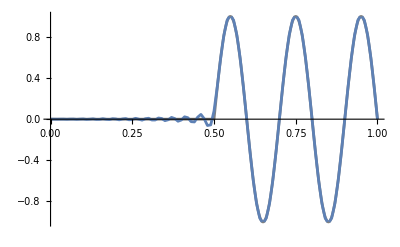

At T = 25.s:

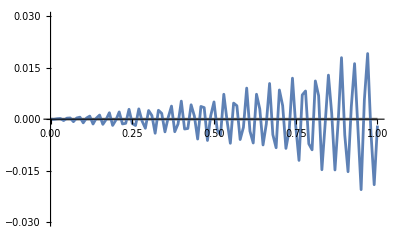

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,1,coeffT4];

RHS=1/h RHSMatrix[n,1,coeffT4];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];

LHS//MatrixForm;
RHS//MatrixForm;

Q=Inverse[LHS].RHS;

reset[]

updateFunction[10/Δt,Q];
plotFunction[{-1,1}]

reset[]

updateFunction[25/Δt,Q];
plotFunction[{-0.03,0.03}]
```

### T6 Boundary Conditions (Fixed Left)

At T = 10.s:

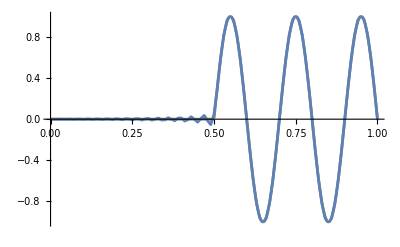

At T = 25.s:

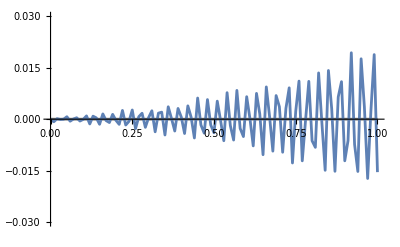

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,2,coeffT6];

RHS=1/h RHSMatrix[n,2,coeffT6];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
RHS//MatrixForm;

Q=Inverse[LHS].RHS;

reset[]

updateFunction[10/Δt,Q];
plotFunction[{-1,1}]

reset[]

updateFunction[25/Δt,Q];
plotFunction[{-0.03,0.03}]
```

### T8 Boundary Conditions (Fixed Left)

At T = 10.s:

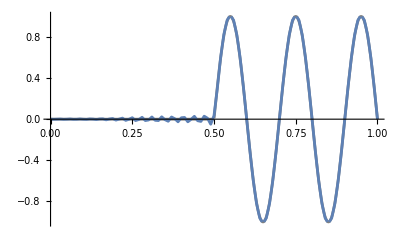

At T = 25.s:

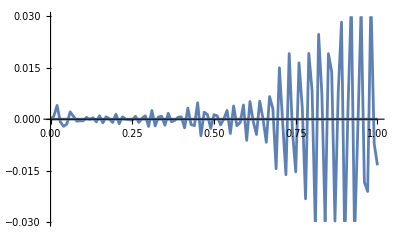

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,3,coeffT8];

RHS=1/h RHSMatrix[n,3,coeffT8];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
RHS//MatrixForm;

Q=Inverse[LHS].RHS;

reset[]

updateFunction[10/Δt,Q];
plotFunction[{-1,1}]

reset[]

updateFunction[25/Δt,Q];
plotFunction[{-0.03,0.03}]
```

### P6 Boundary Conditions (Fixed Left)

At T = 10.s:

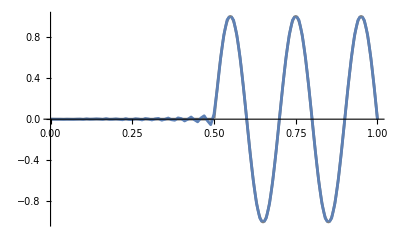

At T = 25.s:

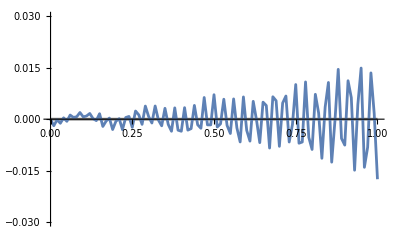

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,1,coeffP6];

RHS=1/h RHSMatrix[n,1,coeffP6];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
RHS//MatrixForm;

Q=Inverse[LHS].RHS;

reset[]

updateFunction[10/Δt,Q];
plotFunction[{-1,1}]

updateFunction[15/Δt,Q];
plotFunction[{-0.03,0.03}]
```

### *P8 Boundary Conditions (Fixed Left)

At T = 10.s:

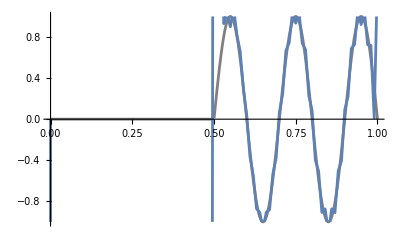

At T = 25.s:

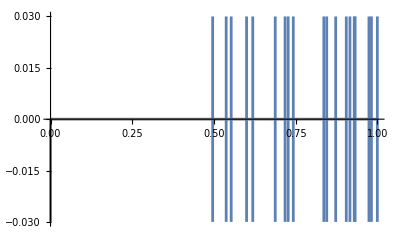

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,2,coeffP8];

RHS=1/h RHSMatrix[n,2,coeffP8];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
h RHS//MatrixForm;

Q=Inverse[LHS].RHS;

reset[]

updateFunction[10/Δt,Q];
plotFunction[{-1,1}]


updateFunction[15/Δt,Q];
plotFunction[{-0.03,0.03}]
```

### *P10 Boundary Conditions (Fixed Left)

At T = 10.s:

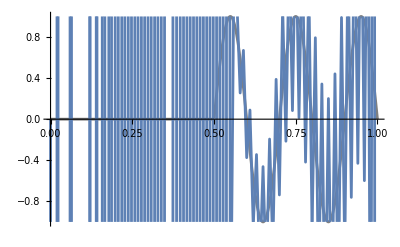

At T = 25.s:

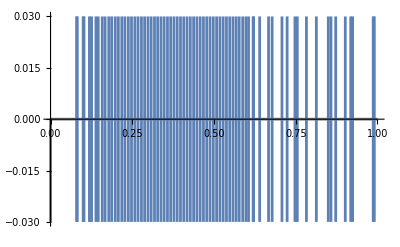

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,3,coeffP10];

RHS=1/h RHSMatrix[n,3,coeffP10];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
h RHS//MatrixForm;

Q=Inverse[LHS].RHS;

reset[]

updateFunction[10/Δt,Q];
plotFunction[{-1,1}]


updateFunction[15/Δt,Q];
plotFunction[{-0.03,0.03}]
```

### *P12 Boundary Conditions (Fixed Left)

At T = 10.s:

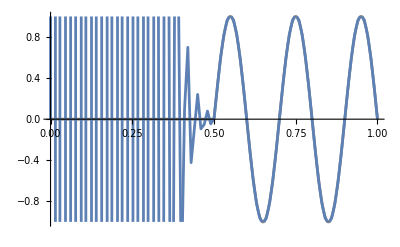

At T = 25.s:

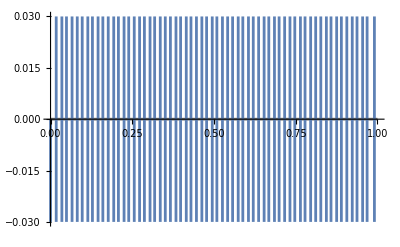

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,4,coeffP12];

RHS=1/h RHSMatrix[n,4,coeffP12];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
RHS//MatrixForm;

Q=Inverse[LHS].RHS;

reset[]

updateFunction[10/Δt,Q];
plotFunction[{-1,1}]

reset[]

updateFunction[25/Δt,Q];
plotFunction[{-0.03,0.03}]
```

## Eigenvalue Spectra

### Eigenvalue Spectra T4 (Periodic)

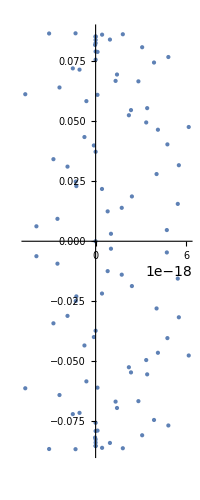

```mathematica
Clear[LHS,RHS,Q];

LHS=PeriodicLHS[n,coeffT4];

RHS=PeriodicRHS[n,coeffT4];

(*LHS=InsideOneSidedBoundaryLHS[LHS,70,1,coeffT4];
RHS=1/h InsideOneSidedBoundaryRHS[RHS,70,1,coeffT4];*)

LHS//MatrixForm;
RHS//MatrixForm;

Q=-waveSpeed*Inverse[LHS].RHS;

eig=Eigenvalues[Q];

ComplexListPlot[eig,PlotRange->All,PlotStyle->{PointSize->Medium},AspectRatio->Full]
```

### Eigenvalue Spectra T8 (Periodic)

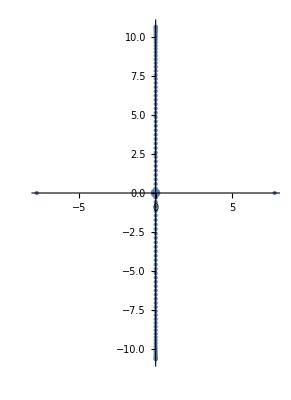

```mathematica
Clear[LHS,RHS,Q];

LHS=PeriodicLHS[n,coeffT8];

RHS=PeriodicRHS[n,coeffT8];

LHS=InsideOneSidedBoundaryLHS[LHS,70,3,coeffT8];
RHS=1/h InsideOneSidedBoundaryRHS[RHS,70,3,coeffT8];

LHS//MatrixForm;
RHS//MatrixForm;

Q=-waveSpeed*Inverse[LHS].RHS;

eig=Eigenvalues[Q];

ComplexListPlot[eig,PlotRange->All,PlotStyle->{PointSize->Medium},AspectRatio->Full]
```

### Eigenvalue Spectra T4 (Fixed Left)

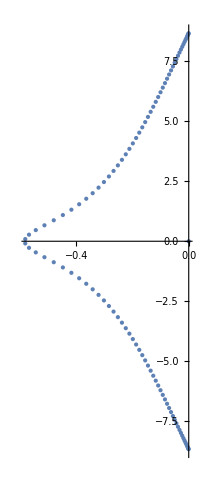

```mathematica
Clear[LHS,RHS,Q,eig];

LHS=LHSMatrix[n,1,coeffT4];

RHS=1/h RHSMatrix[n,1,coeffT4];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];

LHS//MatrixForm;
RHS//MatrixForm;

Q=-waveSpeed*Inverse[LHS].RHS;

eig=Eigenvalues[Q];

ComplexListPlot[eig,PlotRange->All,PlotStyle->{PointSize->Medium},AspectRatio->Full]
```

### Eigenvalue Spectra T6 (Fixed Left)

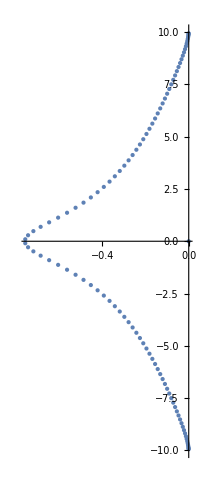

```mathematica
Clear[LHS,RHS,Q,eig];

LHS=LHSMatrix[n,2,coeffT6];

RHS=1/h*RHSMatrix[n,2,coeffT6];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
RHS//MatrixForm;

Q=-waveSpeed*Inverse[LHS].RHS;

eig=Eigenvalues[Q];

ComplexListPlot[eig,PlotRange->All,PlotStyle->{PointSize->Medium},AspectRatio->Full]
```

### Eigenvalue Spectra T8 (Fixed Left)

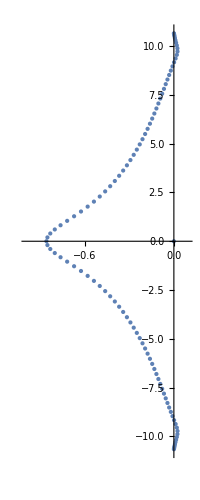

```mathematica
Clear[LHS,RHS,Q,eig];

LHS=LHSMatrix[n,3,coeffT8];

RHS=1/h*RHSMatrix[n,3,coeffT8];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
RHS//MatrixForm;

Q=-waveSpeed*Inverse[LHS].RHS;

eig=Eigenvalues[Q];

ComplexListPlot[eig,PlotRange->{-1,0.1},PlotStyle->{PointSize->Medium},AspectRatio->Full]
```

### Eigenvalue Spectra P6 (Fixed Left)

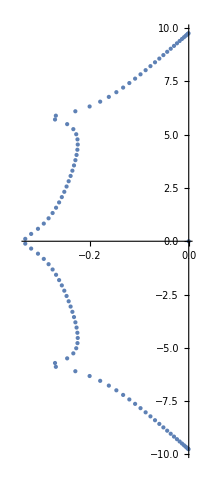

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,1,coeffP6];

RHS=1/h RHSMatrix[n,1,coeffP6];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
RHS//MatrixForm;

Q=-waveSpeed*Inverse[LHS].RHS;

eig=Eigenvalues[Q];

ComplexListPlot[eig,PlotRange->All,PlotStyle->{PointSize->Medium},AspectRatio->Full]
```

### *Eigenvalue Spectra P8 (Fixed Left)

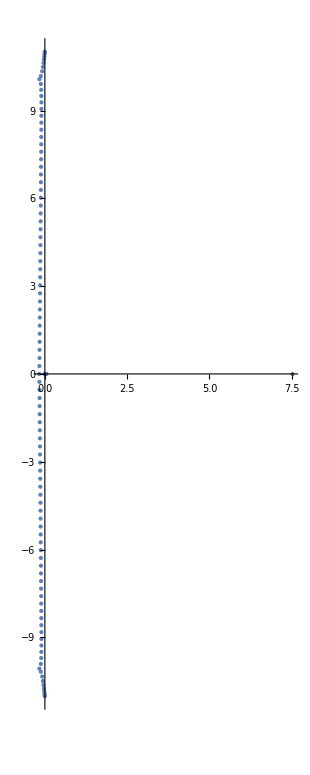

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,2,coeffP8];

RHS=1/h RHSMatrix[n,2,coeffP8];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
RHS//MatrixForm;

Q=-waveSpeed*Inverse[LHS].RHS;

eig=Eigenvalues[Q];

ComplexListPlot[eig,PlotRange->All,PlotStyle->{PointSize->Medium},AspectRatio->Full]
```

### *Eigenvalue Spectra P10 (Fixed Left)

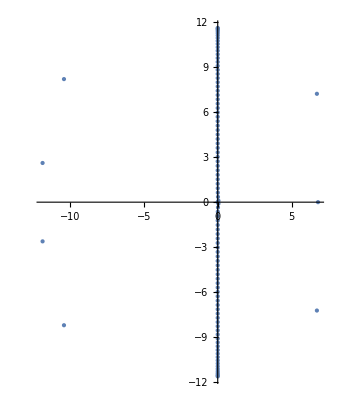

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,3,coeffP10];

RHS=1/h RHSMatrix[n,3,coeffP10];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
RHS//MatrixForm;

Q=-waveSpeed*Inverse[LHS].RHS;

eig=Eigenvalues[Q];

ComplexListPlot[eig,PlotRange->All,PlotStyle->{PointSize->Medium},AspectRatio->Full]
```

### *Eigenvalue Spectra P12 (Fixed Left)

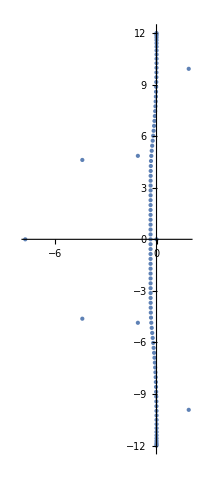

```mathematica
Clear[LHS,RHS,Q,eig];

LHS=LHSMatrix[n,4,coeffP12];

RHS=1/h RHSMatrix[n,4,coeffP12];

(*Set Dirichlet Boundaries on the Left Side*)
LHS=DirichletBoundary[LHS,True,True,False];
RHS=DirichletBoundary[RHS,False,True,False];


LHS//MatrixForm;
RHS//MatrixForm;

Q=-waveSpeed*Inverse[LHS].RHS;

eig=Eigenvalues[Q];

ComplexListPlot[eig,PlotRange->All,PlotStyle->{PointSize->Medium},AspectRatio->Full]
```

## Diffusion Equation

### Diffusion Equation Setup

```mathematica
Clear[Δt,σ,n,h,timeVal,solution,ϕ,reset,updateFunction,plotFunction];

(*Initialize Parameters*)
Δt=0.0001;
σ=2;
n=100;
h=1/(n-1);
timeVal=0;

(*Analytic Solution*)
solution[x_,t_]:=Exp[-2 t] Sin[x];

(*Initial Condition*)
ϕ=Array[Sin[#]&,n,{0,2π}];

reset[]:=Module[{},
timeVal=0;
ϕ=Array[Sin[#]&,n,{0,2π}];
]

updateFunction[steps_,Q_]:=Module[{σtQ},
σtQ=σ Δt Q;
For[i=0,i<steps,i++,
timeVal+=Δt;
ϕ=ϕ+σtQ.ϕ;
];
]

plotFunction[range_]:=Module[{},
normalizePlot={};
For[i=1,i<=n,i++,AppendTo[normalizePlot,{2π(i-1)/(n-1),ϕ[[i]]}]];
Print["At T = "<>ToString[timeVal]<>"s:"];
Show[Plot[solution[x,timeVal],{x,0,2π},PlotRange->range,PlotStyle->Gray],
ListPlot[normalizePlot,PlotRange->range,Joined->True]]
]
```

### T4 Heat Equation

At T = 0.0015s:

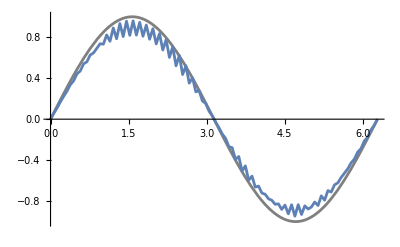

```mathematica
Clear[LHS,RHS,Q];

LHS=LHSMatrix[n,1,coeffT42D];
LHS=DirichletBoundary[LHS,True,True,True];

RHS=h^-2 RHSMatrix2D[n,1,coeffT42D];

RHS=DirichletBoundary[RHS,False,True,True];


LHS//MatrixForm;
RHS*h^2//MatrixForm;

Q=Inverse[LHS].RHS;

reset[]

updateFunction[0.0015/Δt,Q];
plotFunction[{-1,1}]
```